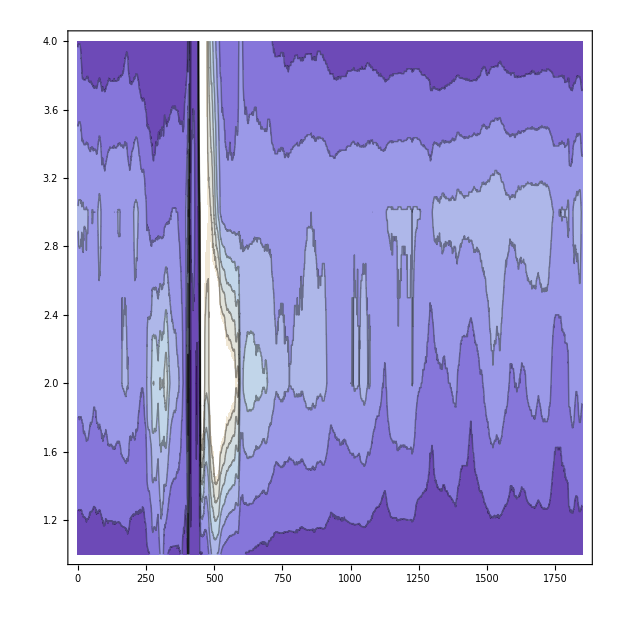

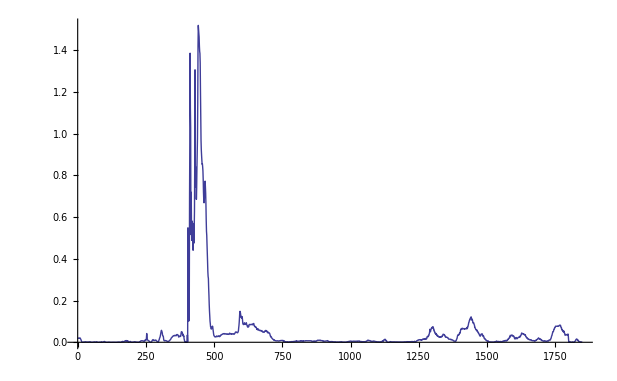

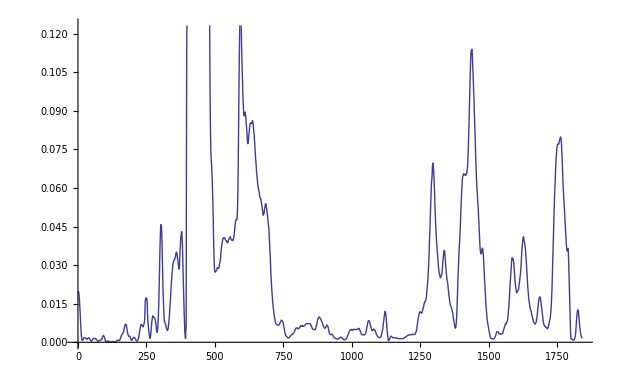

```mathematica
ClearAll[ComputeCentroids,data,data3,data2,cl2,numClusters,startIdx,endIdx,MinDist,centers];

numClusters=4;
startIdx=5;
endIdx=8;

ComputeCentroids[clusteringComponents_,data_,numClusters_]:=(
centers=Reap[
For[i=1,i≤numClusters,i++,(
Clear[centroid,cnt];
centroid=Table[0,{i,endIdx-startIdx+1}];

cnt=0;
For[j=1,j≤Length[data],j++,(
If[clusteringComponents[[j]]==i,(
centroid+=data[[j]];
cnt++;
)];
)]; (*of For - data*)
centroid/=cnt;
Sow[centroid,sowcentroid]
(*Print["Centroid for cluster ",i,  " is ", centroid];
Print["Sample distance: ", ToString[EuclideanDistance[data[[1]],centroid]//N]];*)

)]; (*of For-numClusters *)

,sowcentroid];
Return[Flatten[centers[[2]],1]];
);

MinDist[list_,data_]:=(
ret=100000000000000;
For[j=1,j≤Length[list],j++,(
Clear[dist];
dist=CorrelationDistance[list[[j]],data];
ret=Min[ret,dist];

)];
Return[ret];
);
(*Funktioniert aus irgend einem Grund nicht ...*)
MinDist2[l_,data_]:=(
distances=Map[CosineDistance[l,#]&,data];
distances=(CosineDistance[l,#]&)/@data;
Print[distances//N];
Return[Min[distances]];
);

data=(Import["M:\\Proband1\\00506534Schluck7.ASC.data\\data.csv","Data","HeaderLines"->0]);
data2=data[[1;;400,startIdx;;endIdx]];
data3=data[[All,startIdx;;endIdx]];


(*cl = FindClusters[data2,5(*, Method->"Optimize"*)]; *)
cl2=ClusteringComponents[data2,numClusters,1,DistanceFunction->CorrelationDistance,Method->"KMeans"];
centers=ComputeCentroids[cl2,data2,numClusters];
centroidList=Table[centers[[cl2[[i]]]],{i,1,Length[cl2]}];
(*,PlotStyle->{{Thick,Red},{Thick,Green}} *)

(* ParallelMap[MinDist[centers,#]&,data3[[1;;100,All]]] *)


ListContourPlot[data3//Transpose]
(*ListPlot[Flatten[cl2,0]]*)
(*ListContourPlot[centroidList//Transpose] *)
(*Joined->True *)
ListPlot[ParallelMap[MinDist[centers,#]&,data3],Joined->True,PlotRange->All]
ListPlot[MovingAverage[ParallelMap[MinDist[centers,#]&,data3],9],Joined->True]
```